## Start up

### Path Adjustment

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

```mathematica
<<LocalStartup`;
```

Get::noopen: Cannot open LocalStartup`.

#### Startup checks

### Package Loading

```mathematica
<<UtilizedResourceFunc`;
```

```mathematica
<<PlotMatexFormatting`;
```

```mathematica
<<ExtFileLoading`;
```

```mathematica
<<ExternalEvaluatorFuncs`;
```

```mathematica
cdJulia[Directory[]];
addJuliaPathSrc[];
```

```mathematica
<<ArrayManip`;
```

```mathematica
<<FileNaming`;
```

```mathematica
<<StrIOManip`;
```

```mathematica
<<FileSaving`;
```

```mathematica
<<MCLoops`;
```

```mathematica
<<Geo3d`;
```

```mathematica
<<ImgProcessing`;
```

```mathematica
<<LocalFileNameRef`;
```

### Reload external evaluator

```mathematica
<<ExternalEvaluatorLoad`;
```

### Directory check

```mathematica
$Path
```

{C:\Users\ohdrawnil\AppData\Roaming\Wolfram\DocumentationIndices,C:\Program Files\Wolfram Research\Wolfram\14.1\SystemFiles\Links,C:\Users\ohdrawnil\AppData\Roaming\Wolfram\Kernel,C:\Users\ohdrawnil\AppData\Roaming\Wolfram\Autoload,C:\Users\ohdrawnil\AppData\Roaming\Wolfram\Applications,C:\ProgramData\Wolfram\Kernel,C:\ProgramData\Wolfram\Autoload,C:\ProgramData\Wolfram\Applications,.,C:\Users\ohdrawnil,C:\Program Files\Wolfram Research\Wolfram\14.1\AddOns\Packages,C:\Program Files\Wolfram Research\Wolfram\14.1\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Wolfram\14.1\AddOns\Autoload,C:\Program Files\Wolfram Research\Wolfram\14.1\AddOns\Applications,C:\Program Files\Wolfram Research\Wolfram\14.1\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Wolfram\14.1\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Wolfram\14.1\Documentation\English\System,C:\Program Files\Wolfram Research\Wolfram\14.1\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Wolfram\14.1\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

```mathematica
Remove[texStyle]
```

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Binegativity

```mathematica
NotebookDirectory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Binegativity\

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Binegativity

## BiNeg min coeff

```mathematica
minBiNegLst=readJuliaVar["toric2d_minBiNeg.jld2","minCoeffBiLst"];
```

```mathematica
lambMax=2;
lambStep=0.1;
```

```mathematica
lambALst=Range[lambStep,lambMax,lambStep];
lambBLst=Range[lambStep,lambMax,lambStep];
```

```mathematica
minBiNegLst//MatrixForm
```

(4.32524 | 3.20421 | 2.37374 | 2.14785 | 1.59117 | 1.5897 | 2.05085 | 2.4843 | 2.77235 | 3.01881 | 3.30287 | 3.62548 | 3.98843 | 4.39431 | 4.8464 | 5.34864 | 5.90564 | 6.52265 | 7.20561 | 7.96119
3.06436 | 2.41367 | 2.50888 | 2.4473 | 3.17156 | 3.49152 | 3.84866 | 4.24597 | 4.68699 | 5.17583 | 5.71715 | 6.31618 | 6.97879 | 7.71152 | 8.52164 | 9.41719 | 10.4071 | 11.5013 | 12.7106 | 14.0472
2.10943 | 2.33128 | 2.91574 | 3.37848 | 3.84943 | 4.33994 | 4.85983 | 5.41796 | 6.0226 | 6.6818 | 7.40364 | 8.19645 | 9.06897 | 10.0305 | 11.0912 | 12.2619 | 13.5547 | 14.9826 | 16.5601 | 18.303
1.72561 | 2.05593 | 3.05441 | 3.65318 | 4.24299 | 4.60969 | 4.84037 | 5.16118 | 5.56452 | 6.04643 | 6.6058 | 7.24384 | 7.96367 | 8.7701 | 9.6694 | 10.6693 | 11.7787 | 13.0081 | 14.3692 | 15.8753
1.12648 | 2.34781 | 3.0667 | 3.73887 | 4.39112 | 5.04482 | 5.71754 | 6.42417 | 7.17783 | 7.99052 | 8.87371 | 9.83868 | 10.8969 | 12.0604 | 13.3417 | 14.7544 | 16.3132 | 18.0341 | 19.9346 | 22.0341
0.968618 | 2.22451 | 2.97569 | 3.49599 | 4.34185 | 5.00877 | 5.69134 | 6.40531 | 7.16446 | 7.98129 | 8.86761 | 9.83498 | 10.8951 | 12.06 | 13.3425 | 14.7562 | 16.3159 | 18.0376 | 19.9389 | 22.039
1.05276 | 2.0658 | 2.80728 | 3.09269 | 4.1457 | 4.79484 | 5.45701 | 6.14789 | 6.88113 | 7.66901 | 8.52313 | 9.45474 | 10.4752 | 11.5962 | 12.8301 | 14.1901 | 15.6904 | 17.3463 | 19.175 | 21.1948
1.05412 | 1.88384 | 2.58695 | 2.72581 | 3.8503 | 4.46055 | 5.08177 | 5.7289 | 6.41489 | 7.15139 | 7.94932 | 8.81929 | 9.77197 | 10.8183 | 11.9699 | 13.239 | 14.6389 | 16.1841 | 17.8904 | 19.775
0.956168 | 1.6903 | 2.33742 | 2.38877 | 3.4968 | 4.05539 | 4.62327 | 5.21423 | 5.8402 | 6.51189 | 7.23933 | 8.03224 | 8.90037 | 9.85374 | 10.9029 | 12.0591 | 13.3344 | 14.742 | 16.2963 | 18.013
0.834013 | 1.4952 | 2.0773 | 2.07921 | 3.1182 | 3.61888 | 4.12744 | 4.65632 | 5.21625 | 5.81687 | 6.46718 | 7.17589 | 7.95174 | 8.8037 | 9.7412 | 10.7743 | 11.9138 | 13.1715 | 14.5603 | 16.0942
0.721776 | 1.30639 | 1.82064 | 1.79679 | 2.7391 | 3.18039 | 3.62838 | 4.09406 | 4.58693 | 5.1155 | 5.68768 | 6.31119 | 6.99371 | 7.74314 | 8.56779 | 9.4765 | 10.4788 | 11.5851 | 12.8066 | 14.1557
0.619957 | 1.12936 | 1.57721 | 1.54179 | 2.37643 | 2.76015 | 3.14955 | 3.55422 | 3.98241 | 4.44155 | 4.93852 | 5.48002 | 6.07275 | 6.72356 | 7.43968 | 8.22877 | 9.09914 | 10.0598 | 11.1205 | 12.292
0.528814 | 0.967526 | 1.35309 | 1.31424 | 2.04078 | 2.3708 | 2.70561 | 3.05349 | 3.42154 | 3.81614 | 4.24324 | 4.70858 | 5.21791 | 5.77715 | 6.39249 | 7.07054 | 7.81841 | 8.64384 | 9.55525 | 10.5619
0.448265 | 0.822557 | 1.15142 | 1.11355 | 1.73779 | 2.01908 | 2.30443 | 2.60087 | 2.91446 | 3.25066 | 3.61452 | 4.01095 | 4.44485 | 4.92126 | 5.44545 | 6.02306 | 6.66015 | 7.36329 | 8.13969 | 8.99723
0.377906 | 0.694816 | 0.97322 | 0.93848 | 1.46949 | 1.70752 | 1.94894 | 2.19973 | 2.46502 | 2.74941 | 3.05719 | 3.39252 | 3.75954 | 4.16251 | 4.60589 | 5.09445 | 5.63332 | 6.22806 | 6.88477 | 7.61009
0.31708 | 0.583753 | 0.817998 | 0.787265 | 1.23549 | 1.4357 | 1.63876 | 1.84967 | 2.07278 | 2.31194 | 2.57077 | 2.85276 | 3.16139 | 3.50025 | 3.8731 | 4.28393 | 4.73707 | 5.23719 | 5.78942 | 6.39935
0.264964 | 0.488238 | 0.684349 | 0.657777 | 1.03383 | 1.20142 | 1.37137 | 1.5479 | 1.73463 | 1.93479 | 2.1514 | 2.38739 | 2.64569 | 2.92927 | 3.2413 | 3.58513 | 3.96435 | 4.38289 | 4.84503 | 5.35547
0.220651 | 0.406826 | 0.570343 | 0.547717 | 0.861723 | 1.00144 | 1.14312 | 1.29028 | 1.44594 | 1.6128 | 1.79337 | 1.99009 | 2.2054 | 2.4418 | 2.7019 | 2.98851 | 3.30462 | 3.65351 | 4.03875 | 4.46425
0.183215 | 0.337938 | 0.473826 | 0.454762 | 0.715962 | 0.832058 | 0.949791 | 1.07207 | 1.20141 | 1.34005 | 1.49009 | 1.65355 | 1.83245 | 2.02887 | 2.24499 | 2.48313 | 2.74578 | 3.03568 | 3.35577 | 3.70931
0.15176 | 0.279995 | 0.392617 | 0.376672 | 0.593288 | 0.689501 | 0.787068 | 0.888404 | 0.995587 | 1.11048 | 1.23481 | 1.37027 | 1.51852 | 1.6813 | 1.86039 | 2.05774 | 2.2754 | 2.51563 | 2.78088 | 3.07386)

```mathematica
minBiNegData=Table[{lambALst⟦iA⟧,lambBLst⟦iB⟧,minBiNegLst⟦iA,iB⟧},{iA,1,Length[lambALst]},{iB,1,Length[lambBLst]}];
minBiNegDataFlt=Flatten[minBiNegData,1];
```

```mathematica
minBiNegDataFlt//Dimensions
```

{400,3}

```mathematica
lambXYLab=matexLstFunc[{"\\lambda_A","\\lambda_B"},labMag];
```

```mathematica
lambXYLab
```

{-Graphics-,-Graphics-}

```mathematica
numL=3;
labEigValRaw="\\min \\mathrm{eigval}\\left( \\left| \\rho^{\\Gamma} \\right|^{\\Gamma} \\right)";
figLab=MaTeX[labEigValRaw<>",\,"<>"L="<>ToString[numL],Magnification->labMag];
labEigVal=MaTeX[labEigValRaw,Magnification->labMag];
```

```mathematica
figLab
```

-Graphics-

```mathematica
labEigVal
```

-Graphics-

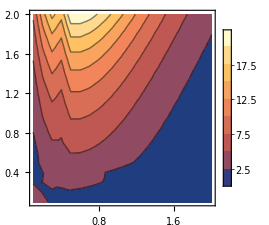

```mathematica
ListContourPlot[minBiNegDataFlt,PlotLegends->Automatic,PlotRangePadding->None,BaseStyle->texStyle,ImageSize->8cm,FrameLabel->lambXYLab,PlotLabel->figLab]
```

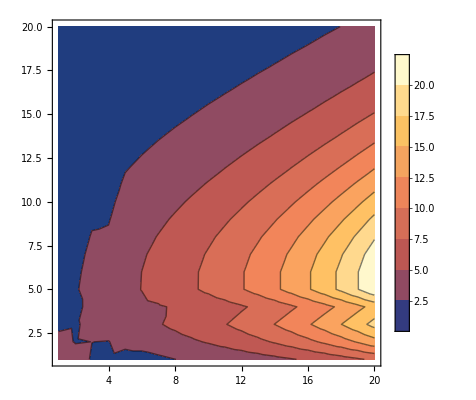

```mathematica
ListContourPlot[minBiNegLst,PlotLegends->Automatic]
```

```mathematica
ListPlot3D[minBiNegDataFlt,BaseStyle->texStyle,ImageSize->10cm,AxesLabel->lambXYLab~Join~{labEigVal},PlotLabel->figLab]
```

-Graphics3D-

```mathematica
ListPlot3D[minBiNegLst]
```

-Graphics3D-

## Ising Testing

```mathematica
mArr=Transpose[readJuliaVar["mArr.jld2","mArr"]];
```

```mathematica
hLst=Range[-2,2,0.01];
```

```mathematica
ListPlot[hLst
```

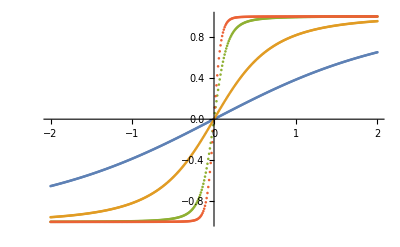

```mathematica
ListPlot[{hLst,#}ᵀ&/@mArr]
```

```mathematica
matArr
```

```mathematica
evalJulia["pwd()"]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Binegativity

```mathematica
Remove[addJuliaPathSrc]
```

## Misc

```mathematica
ma
```